```mathematica
listAlpha={}
listBeta={}
foo[n_]:=
Module[
{
iterator=1,
listA={},
listB={}
},
While[
iterator<10000,
If[
Mod[iterator,6]==0,
AppendTo[listA,iterator];
If[RandomInteger[{1,6}]==6,
AppendTo[listB,iterator]
],
If[RandomInteger[{1,6}]==6,
AppendTo[listB,iterator]
]
];
iterator=iterator+1
];
{listA, listB, Length@listA,Length@listB}
]
```

{}

{}

```mathematica
Mod[4,2]
```

0

```mathematica
RandomInteger[{1,6}]
```

6

```mathematica
listA
```

{}

```mathematica
foo
```

```mathematica
listA
```

{}

```mathematica
results:=

Module[
{
iterator=1,
sentinel={},
listOne={},
listTwo={}

},
While[
iterator<100,
sentinel=foo[1];
AppendTo[listOne,sentinel[[3]]];
AppendTo[listTwo,sentinel[[4]]];
iterator=iterator+1
];
{listOne,listTwo}
]
```

```mathematica
results
```

{{1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666,1666},{1671,1675,1698,1756,1604,1681,1639,1649,1621,1658,1684,1680,1648,1650,1684,1652,1714,1654,1719,1668,1662,1663,1633,1656,1719,1667,1635,1659,1640,1672,1681,1639,1641,1720,1648,1670,1734,1659,1635,1678,1681,1674,1677,1625,1658,1652,1690,1674,1708,1652,1659,1642,1706,1666,1675,1655,1674,1687,1658,1732,1678,1700,1714,1652,1705,1634,1675,1665,1608,1679,1680,1696,1678,1697,1685,1650,1652,1668,1751,1597,1598,1685,1605,1660,1644,1633,1689,1620,1643,1682,1679,1627,1665,1585,1682,1711,1624,1649,1678}}

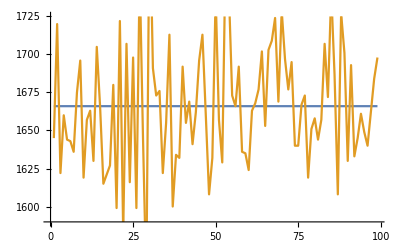

```mathematica
ListLinePlot@results
```

```mathematica
Module[
{
iterator=1,
listA={},
listB={}
},
While[
iterator<10,
Print["foo"];
iterator=iterator+1
]
]
```

foo

foo

foo

«6 more identical outputs»

```mathematica
foo
```

foo

```mathematica
Four
```

```mathematica
integrateThis:=ListFourierSequenceTransform[results[[2]],t]
```

```mathematica
Abs@N@Integrate[integrateThis,{t,0,100}]/1000

(*this is fourier fitting (kind of )*)
```

156.693

```mathematica
Abs[158.06115620185602-7.480106432922328 ⅈ]
```

158.238

```mathematica
Conju
```

```mathematica
resultsB:=

Module[
{
iterator=1,
sentinel={},
listOne={},
listTwo={}

},
While[
iterator<100,
sentinel=foo[1];
AppendTo[listOne,sentinel[[3]]-sentinel[[4]]];
iterator=iterator+1
];
{listOne,N@Total@listOne/Length@listOne}
]
```

```mathematica
resultsB
```

{{60,-23,-20,-21,29,-34,-23,9,15,76,17,-18,15,-13,-19,24,57,-26,-15,-13,15,-56,14,-72,-13,34,-48,-10,-35,55,46,-24,-35,48,-52,-42,-8,53,0,17,-38,83,-2,-9,70,20,-8,19,8,-52,-23,11,-44,-3,23,-56,39,14,20,7,-61,-50,-12,-45,-13,39,-15,-14,5,-28,-10,-19,-11,35,20,-4,7,-19,49,32,26,32,38,-20,-20,54,-59,41,32,72,7,14,-12,-40,-20,-12,-59,-40,108},0.717172}